## Generate training data for DCNN

### Wolfram Classes of ECAs

```mathematica
CAclasses = {1,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,3,2,2,2,3,2,2,2,2,2,2,2,3,2,1,2,2,2,2,2,2,2,1,3,2,2,2,3,2,2,2,2,2,2,2,2,4,2,2,2,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,3,2,2,3,3,2,2,2,2,2,1,3,2,2,2,3,3,2,2,3,3,3,2,2,4,2,2,2,2,2,2,2,2,2,3,3,3,2,4,2,3,2,1,3,2,2,2,2,2,3,1,4,2,2,2,2,2,2,2,2,3,4,2,3,3,3,2,3,2,2,2,2,2,2,1,3,2,2,2,3,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,2,2,2,2,2,2,2,1,4,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,1,1,2,2,1,1,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1};
```

### Functions for creating net and random datasets (ECAs, all 4 classes)

```mathematica
RandomRuleC[n_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[n,RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
netC[W_Integer,H_Integer]:=NetInitialize@NetChain[{ConvolutionLayer[16,{2,3}],Ramp,PoolingLayer[{H,W}-{1,2}],FlattenLayer[],LinearLayer[256],SoftmaxLayer[]},"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[0,255]}]]
netTwoCC[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[16,{2,3}],"ramp1"-> Ramp, "conv3"-> ConvolutionLayer[16,{2,3}],"ramp2"-> Ramp,"pooling"-> PoolingLayer[{H,W}-{2,4}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
dataC[W_Integer,H_Integer,n_Integer]:=Table[RandomRuleC[i,W,H]->CAclasses[[i+1]],{i,RandomChoice[Range[0,255],n]}]
```

```mathematica
netThreeCC[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[16,{2,3}],"ramp1"-> Ramp, "conv2"-> ConvolutionLayer[16,{2,3}],"ramp2"-> Ramp,"conv3"->ConvolutionLayer[16,{2,3}],"ramp3"->Ramp,"pooling"-> PoolingLayer[{H,W}-{4,8}],"flatten"-> FlattenLayer[],"linear"-> 512,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

```mathematica
netThreeCC1024[W_Integer,H_Integer]:=NetInitialize@NetChain[<|"conv1"-> ConvolutionLayer[16,{2,3}],"ramp1"-> Ramp, "conv2"-> ConvolutionLayer[16,{2,3}],"ramp2"-> Ramp,"conv3"->ConvolutionLayer[16,{2,3}],"ramp3"->Ramp,"pooling"-> PoolingLayer[{H,W}-{4,8}],"flatten"-> FlattenLayer[],"linear"-> 1024,"linear2"-> 4,"softmax"-> SoftmaxLayer[]|>,"Input"->NetEncoder[{"Image",{W,H}}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
```

### Functions for creating datasets (1D totalistic CAs)

#### k=3, r=1 totalistic (class 4 only)

```mathematica
gen3TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {3,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data3T2C[W_Integer,H_Integer,n_Integer]:=Table[gen3TC[i,W,H]->4,{i,RandomChoice[{1635,1815,2007,2043,2049,1388,1041},n]}]
```

#### k=4, r=1 totalistic (class 4 only, 1 example)

```mathematica
gen4TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {4,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data4TC[W_Integer,H_Integer,n_Integer]:=Table[gen4TC[1004600,W,H]->4,n]
```

#### k=2, r=2 totalistic (all 4 classes)

```mathematica
gen2r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {2,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data2r2c4C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->4,{i,RandomChoice[{20,52},n]}]
data2r2c3C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->3,{i,RandomChoice[{2,6,10,12,14,18,22,26,28,30,34,38,42,44,46,50},n]}]
data2r2c2C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->2,{i,RandomChoice[{8,24,56},n]}]
data2r2c1C[W_Integer,H_Integer,n_Integer]:=Table[gen2r2C[i,W,H]->1,{i,RandomChoice[{0,4,16,32,36,40,48,54,58,60,62},n]}]
genData2r2C[W_Integer,H_Integer,n_Integer]:=Join[data2r2c4C[W,H,n], data2r2c3C[W,H,n],data2r2c2C[W,H,n],data2r2c1C[W,H,n]]
```

#### k=5, r=1 totalistic (class 4 only)

```mathematica
gen5T4C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {5,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data5T4C[n_Integer,W_Integer,H_Integer]:=Table[gen5T4C[i,W,H]->4,{i,RandomChoice[{781130654,772514435,1151319452,309095787,880862046,973835714,779446817,345466505,535500975,793363571,1052373865,455984785,339227109,1050973846,513368817,91315820,113925357},n]}]
```

### k=5, r=1 totalistic (classes 2/3/4)

```mathematica
gen5TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {5,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data5T4CC[W_Integer,H_Integer,n_Integer]:=Table[gen5TC[i,W,H]->4,{i,RandomChoice[{644218533,491739943,6889640,986144962,1099816682,988971204,300829994,272622024,304100638,626595633},n]}]
data5T3CC[W_Integer,H_Integer,n_Integer]:=Table[gen5TC[i,W,H]->3,{i,RandomChoice[{889082395,541068260,807907479,816180062,650485139,643827745,753940864,871525323,351440311,83501460},n]}]
data5T2CC[W_Integer,H_Integer,n_Integer]:=Table[gen5TC[i,W,H]->2,{i,RandomChoice[{525735659,1022330944,1007796739,495633437,1036827943},n]}]
genData5TCC[W_Integer,H_Integer,n_Integer]:=Join[data5T4CC[W,H,n], data5T3CC[W,H,n],data5T2CC[W,H,n]]
```

### Generate test datasets

#### k=2, r=2 non-totalistic

```mathematica
genk2r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, 2,2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
datak2r2C[W_Integer,H_Integer,n_Integer]:=Table[genk2r2C[i,W,H]->i,{i,RandomChoice[Range[0,4294967295],n]}]
```

#### k=3, r=2 totalistic

```mathematica
genk3r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {3,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
datak3r2C[W_Integer,H_Integer,n_Integer]:=Table[genk3r2C[i,W,H]->i,{i,RandomChoice[Range[0,177146],n]}]
```

#### k=4, r=1 totalistic

```mathematica
genk4r1C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {4,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
datak4r1C[W_Integer,H_Integer,n_Integer]:=Table[genk4r1C[i,W,H]->i,{i,RandomChoice[Range[0,1048575],n]}]
```

#### k=4, r=2 totalistic

```mathematica
genk4r2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {4,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
datak4r2C[W_Integer,H_Integer,n_Integer]:=Table[genk4r2C[i,W,H]->i,{i,RandomChoice[Range[0,4294967295],n]}]
```

#### k=5, r=1 totalistic

```mathematica
gen5T2C[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {5,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data5T2C[n_Integer,W_Integer,H_Integer]:=Table[gen5T2C[i,W,H]->i,{i,RandomChoice[Range[0,1220703125],n]}]
```

#### k=6, r=1 totalistic

```mathematica
gen6TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {6,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple},Frame->False]]
data6TC[n_Integer,W_Integer,H_Integer]:=Table[gen6TC[i,W,H]->i,{i,RandomInteger[2821109907455,n]}]
```

### k=7, r=1 totalistic

```mathematica
gen7TC[p_Integer,W_Integer,H_Integer]:=Image[ArrayPlot[CellularAutomaton[{p, {7,1},1},RandomInteger[1,W],H-1],ImageSize->{W,H},ColorRules->{1->Pink, 2->Blue, 3->Green,4->Orange,5->Red,6->Yellow, 7->Purple,8->Brown},Frame->False]]
data7TC[n_Integer,W_Integer,H_Integer]:=Table[gen7TC[i,W,H]->i,{i,RandomInteger[11398895185373142,n]}]
```

### Create training data for Network III (ECAs; k=2,r=2; k=3, r=1; k=4, r=1; k=5, r=1)

```mathematica
netECA4=netTwoCC[200,120]
```

NetChain[<>]

```mathematica
dataECA4=dataC[200,120,8192];
```

```mathematica
dataTotalistic2BigC=genData2r2C[200,120,1024];
```

```mathematica
dataTotalistic3BigC=data3T2C[200,120,4096];
```

```mathematica
dataTotalistic4BigC=data4TC[200,120,4096];
```

```mathematica
dataTotalistic5BigC=data5T4C[4096,200,120];
```

```mathematica
fullTrainingBigC=Join[dataECA4,dataTotalistic2BigC,dataTotalistic3BigC,dataTotalistic4BigC,dataTotalistic5BigC];
Length[fullTrainingBigC]
RandomSample[fullTrainingBigC,20]
```

24576

{-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→4}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA4=NetTrain[netECA4,fullTrainingBigC,MaxTrainingRounds->10,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory","networkIV"}]
```

NetChain[<>]

```mathematica
Export["netECA6-22may-1.wlnet",netECA6,"WLNet"]
```

netECA6-22may-1.wlnet

### Training Attempt 1

```mathematica
dataECA5=dataC[200,120,2048];
dataTotalistic2BigC2=genData2r2C[200,120,256];
dataTotalistic3BigC2=data3T2C[200,120,1024];
dataTotalistic4BigC2=data4TC[200,120,1024];
dataTotalistic5BigC2=data5T4C[1024,200,120];
fullTrainingBigC2=Join[dataECA5,dataTotalistic2BigC2,dataTotalistic3BigC2,dataTotalistic4BigC2,dataTotalistic5BigC2];
Length[fullTrainingBigC2]
RandomSample[fullTrainingBigC2,20]
```

6144

{-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→1,-Graphics-→4,-Graphics-→4,-Graphics-→1,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→2}

### Training Attempt 2

```mathematica
dataECA6=dataC[200,120,8192];
dataTotalistic2BigC3=genData2r2C[200,120,512];
dataTotalistic3BigC3=data3T2C[200,120,2048];
dataTotalistic4BigC3=data4TC[200,120,2048];
dataTotalistic5BigC3=genData5TCC[200,120,1024];
fullTrainingBigC3=Join[dataECA6,dataTotalistic2BigC3,dataTotalistic3BigC3,dataTotalistic4BigC3,dataTotalistic5BigC3];
Length[fullTrainingBigC3]
RandomSample[fullTrainingBigC3,20]
```

17408

{-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3}

```mathematica
netECA4=NetTrain[netECA4,fullTrainingBigC3,MaxTrainingRounds->12,BatchSize->256*4,TargetDevice->"CPU"]
```

NetChain[<>]

### Training Attempt 3

```mathematica
netECA5=netThreeCC[200,120]
```

NetChain[<>]

```mathematica
netECA5=NetTrain[netECA5,fullTrainingBigC3,MaxTrainingRounds->16,BatchSize->256*4,TargetDevice->"CPU"]
```

NetChain[<>]

### Training Attempt 4

```mathematica
netECA6=netThreeCC1024[200,120]
```

NetChain[<>]

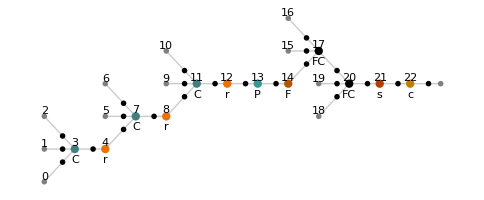

```mathematica
NetInformation[netECA6,"MXNetNodeGraphPlot"]
```

```mathematica
NetInformation[netECA6,"SummaryGraphic"]
```

-Graphics-

```mathematica
netECA6=NetTrain[netECA6,fullTrainingBigC3,MaxTrainingRounds->18,BatchSize->256*4,TargetDevice->"CPU"]
```

NetChain[<>]

### Training Attempt 7

```mathematica
dataECA7=dataC[200,120,8192];
```

```mathematica
dataTotalistic2BigC7=genData2r2C[200,120,4096];
```

```mathematica
dataTotalistic3BigC7=data3T2C[200,120,1024];
```

```mathematica
dataTotalistic4BigC7=data4TC[200,120,1024];
```

```mathematica
dataTotalistic5BigC7=genData5TCC[200,120,4096];
```

```mathematica
fullTrainingBigC7=Join[dataECA7,dataTotalistic2BigC7,dataTotalistic3BigC7,dataTotalistic4BigC7,dataTotalistic5BigC7];
Length[fullTrainingBigC7]
RandomSample[fullTrainingBigC7,20]
```

38912

{-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→1,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→1,-Graphics-→1,-Graphics-→2}

```mathematica
netECA7=netThreeCC1024[200,120]
```

NetChain[<>]

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA7=NetTrain[netECA7,fullTrainingBigC7,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

### Generate test data for Network VII

```mathematica
testDataECABigC=dataC[200,120,1024];
testData2TBigC=genData2r2C[200,120,1024];
testData3TBigC=data3T2C[200,120,1024];
testData4TBigC=data4TC[200,120,1024];
testData5TBigC=genData5TCC[200,120,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2}

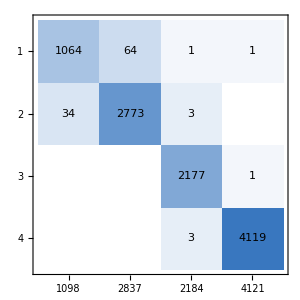
{0.989551,<|1→0.969035,2→0.977441,3→0.996795,4→0.999515|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA7, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA7[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA7[highEntBigC]]
Thread[lowEntBigC->netECA7[lowEntBigC]]
```

{-Graphics-→1,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→1,-Graphics-→2,-Graphics-→3}

{-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4}

```mathematica
testData5kr1C6=data5T2C[20,200,120];
k5r1testC6=Thread[testData5kr1C6->netECA7[Keys@testData5kr1C6,{"TopProbabilities",2}]]
```

{(-Graphics-→743380617)→{2→4.05119×10^-7,4→1.},(-Graphics-→420167147)→{4→4.31548×10^-8,3→1.},(-Graphics-→60914090)→{4→0.00807698,3→0.991923},(-Graphics-→416227792)→{4→0.209166,3→0.790834},(-Graphics-→44277671)→{3→0.108628,4→0.891231},(-Graphics-→1123916113)→{3→0.352268,4→0.647732},(-Graphics-→210080263)→{3→0.0825588,4→0.917441},(-Graphics-→549817328)→{3→0.00303919,4→0.996791},(-Graphics-→14241394)→{3→9.81169×10^-9,4→1.},(-Graphics-→227347521)→{4→0.0000667955,3→0.999933},(-Graphics-→963573258)→{2→0.00405763,4→0.995942},(-Graphics-→468297088)→{4→0.0682615,3→0.931739},(-Graphics-→603744576)→{4→0.407975,3→0.592025},(-Graphics-→727654295)→{4→0.00129026,2→0.998705},(-Graphics-→546899097)→{2→0.000478121,4→0.99947},(-Graphics-→825664550)→{3→1.33098×10^-8,2→1.},(-Graphics-→702688740)→{3→1.70615×10^-6,4→0.999998},(-Graphics-→371146611)→{4→0.488173,3→0.511827},(-Graphics-→408425988)→{4→0.0549904,3→0.945009},(-Graphics-→659605814)→{4→1.87779×10^-6,2→0.999998}}

```mathematica
testData6kr1C6 = data6TC[20,200,120];
k6r1testC6=Thread[testData6kr1C6->netECA7[Keys@testData6kr1C6,{"TopProbabilities",2}]]
```

{(-Graphics-→1041710623193)→{3→0.200591,4→0.799409},(-Graphics-→1541484819676)→{3→0.0000359852,4→0.999964},(-Graphics-→2279554396643)→{4→0.00219543,3→0.997805},(-Graphics-→696224743701)→{4→1.2178×10^-6,3→0.999999},(-Graphics-→1804464290893)→{3→0.00065873,4→0.999341},(-Graphics-→1483771507465)→{3→0.111385,4→0.888608},(-Graphics-→1191969567563)→{4→0.000208525,3→0.999791},(-Graphics-→1762402563208)→{3→0.207857,4→0.792103},(-Graphics-→1071877853786)→{4→7.61569×10^-18,2→1.},(-Graphics-→2704742708932)→{3→0.0000142801,4→0.999986},(-Graphics-→899762013116)→{4→0.00309346,2→0.995696},(-Graphics-→1652190518167)→{4→0.224451,3→0.775549},(-Graphics-→2706717337080)→{3→0.133773,4→0.866227},(-Graphics-→1753827991569)→{3→0.00240432,4→0.997596},(-Graphics-→589132365783)→{4→0.00316477,3→0.996835},(-Graphics-→1408149604868)→{4→0.00162216,3→0.998378},(-Graphics-→1560072159610)→{4→0.0103508,3→0.989649},(-Graphics-→2085943632696)→{4→0.0198733,3→0.980127},(-Graphics-→301381395692)→{2→0.00491467,4→0.995085},(-Graphics-→532232620420)→{3→0.476682,4→0.523318}}

```mathematica
test2Data6kr1C6 = data6TC[20,200,120];
k6r1test2C6=Thread[test2Data6kr1C6->netECA7[Keys@test2Data6kr1C6,{"TopProbabilities",2}]]
```

{(-Graphics-→1399542338855)→{4→2.80487×10^-6,3→0.999997},(-Graphics-→250524360135)→{3→0.00020253,4→0.999746},(-Graphics-→549188432385)→{4→1.4749×10^-7,3→1.},(-Graphics-→1670565958943)→{3→0.453499,4→0.546501},(-Graphics-→1947156561700)→{4→0.000199657,2→0.9998},(-Graphics-→2442596135264)→{3→0.20835,4→0.79165},(-Graphics-→2813741167091)→{4→0.005064,3→0.994936},(-Graphics-→702435762432)→{4→0.161254,2→0.776976},(-Graphics-→56711608319)→{3→0.000159938,4→0.99984},(-Graphics-→954453559728)→{3→0.0436021,4→0.956398},(-Graphics-→1383877623345)→{3→0.0314444,4→0.968535},(-Graphics-→2047441890767)→{4→0.00151694,3→0.998483},(-Graphics-→2135164653304)→{4→0.199021,3→0.800921},(-Graphics-→692379794540)→{3→1.22673×10^-8,4→1.},(-Graphics-→1058788001098)→{3→7.68582×10^-7,2→0.999999},(-Graphics-→2709619897373)→{4→0.000109994,3→0.99989},(-Graphics-→2298811569801)→{4→0.0387178,3→0.961282},(-Graphics-→1843311712861)→{3→0.248157,2→0.749718},(-Graphics-→277609027910)→{3→2.53597×10^-6,4→0.999997},(-Graphics-→2413949709384)→{3→0.0000825846,4→0.999914}}

```mathematica
test3Data6kr1C6 = data6TC[20,200,120];
k6r1test3C6=Thread[test3Data6kr1C6->netECA7[Keys@test3Data6kr1C6,{"TopProbabilities",2}]]
```

{(-Graphics-→2572280477952)→{3→0.00244909,4→0.997551},(-Graphics-→2792470593617)→{3→1.77791×10^-6,4→0.999998},(-Graphics-→2186533635831)→{4→0.0304701,3→0.96953},(-Graphics-→780672051722)→{3→0.00222374,4→0.997775},(-Graphics-→220495815935)→{3→5.85262×10^-7,4→0.999999},(-Graphics-→1032590219492)→{4→2.08993×10^-6,3→0.999998},(-Graphics-→1619491853053)→{4→0.00772504,2→0.992274},(-Graphics-→2270970704726)→{4→0.0047662,3→0.992901},(-Graphics-→2657122596782)→{3→0.392864,4→0.607127},(-Graphics-→1154488446996)→{4→7.03027×10^-6,3→0.999993},(-Graphics-→1971033787025)→{4→0.0000152878,3→0.999985},(-Graphics-→2445830530159)→{4→0.0000522219,3→0.999948},(-Graphics-→1188506090446)→{4→6.07206×10^-6,3→0.999994},(-Graphics-→1286509461709)→{3→0.0000838736,4→0.999915},(-Graphics-→293576881330)→{2→0.000370834,4→0.999442},(-Graphics-→1374554496209)→{4→0.221928,3→0.778071},(-Graphics-→324661610660)→{4→0.208066,3→0.791934},(-Graphics-→1503631290686)→{3→0.0281068,4→0.971357},(-Graphics-→1008611736292)→{3→0.00442699,4→0.995573},(-Graphics-→1171363664378)→{3→0.00220774,4→0.997792}}

### Training Attempt 8

```mathematica
dataECA8=dataC[150,150,8192];
```

```mathematica
dataTotalistic2BigC8=genData2r2C[150,150,4096];
```

```mathematica
dataTotalistic3BigC8=data3T2C[150,150,1024];
```

```mathematica
dataTotalistic4BigC8=data4TC[150,150,1024];
```

```mathematica
dataTotalistic5BigC8=genData5TCC[150,150,4096];
```

```mathematica
fullTrainingBigC8=Join[dataECA8,dataTotalistic2BigC8,dataTotalistic3BigC8,dataTotalistic4BigC8,dataTotalistic5BigC8];
```

```mathematica
Length[fullTrainingBigC8]
RandomSample[fullTrainingBigC8,20]
```

38912

{-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→3,-Graphics-→4,-Graphics-→1}

```mathematica
netECA8=netThreeCC1024[150,150]
```

NetChain[<>]

```mathematica
dir=SetDirectory[NotebookDirectory[]]
```

/Users/thorsilver/Downloads/Wolfram notebooks

```mathematica
netECA8=NetTrain[netECA8,fullTrainingBigC8,MaxTrainingRounds->20,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory",dir}]
```

NetChain[<>]

### Generate test data for Network VIII

```mathematica
testDataECABigC=dataC[150,150,1024];
testData2TBigC=genData2r2C[150,150,1024];
testData3TBigC=data3T2C[150,150,1024];
testData4TBigC=data4TC[150,150,1024];
testData5TBigC=genData5TCC[150,150,1024];
fullTestSetBigC=Join[testDataECABigC,testData2TBigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

10240

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→4,-Graphics-→1,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4}

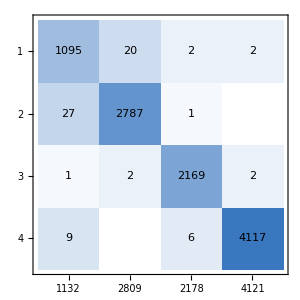
{0.992969,<|1→0.967314,2→0.992168,3→0.995868,4→0.999029|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA8, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA8[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]];
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]];
Thread[highEntBigC->netECA8[highEntBigC]]
Thread[lowEntBigC->netECA8[lowEntBigC]]
```

{-Graphics-→3,-Graphics-→2,-Graphics-→1,-Graphics-→1,-Graphics-→2,-Graphics-→1,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→3}

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3}

```mathematica
testDatak5r1C8=data5T2C[20,150,150];
k5r1testC8=Thread[testDatak5r1C8->netECA8[Keys@testDatak5r1C8,{"TopProbabilities",2}]]
```

{(-Graphics-→351576556)→{3→0.00229393,2→0.99759},(-Graphics-→282743455)→{4→0.000314574,3→0.999685},(-Graphics-→1104975539)→{4→0.0115304,3→0.988441},(-Graphics-→9756314)→{2→0.0211805,3→0.97881},(-Graphics-→258637104)→{4→0.0564866,3→0.943513},(-Graphics-→460506861)→{4→8.89447×10^-12,3→1.},(-Graphics-→1058803988)→{3→0.0235174,4→0.976483},(-Graphics-→40089852)→{3→0.000167637,4→0.999832},(-Graphics-→684452557)→{3→0.00869475,4→0.9913},(-Graphics-→267988422)→{4→0.16938,3→0.828219},(-Graphics-→1011449557)→{4→0.00685299,3→0.992847},(-Graphics-→29897960)→{3→4.48256×10^-10,4→1.},(-Graphics-→155874880)→{3→0.260244,2→0.739487},(-Graphics-→998880469)→{2→0.0447028,4→0.955125},(-Graphics-→820788605)→{3→0.000069524,4→0.999931},(-Graphics-→317899467)→{4→0.00138674,3→0.998613},(-Graphics-→336374761)→{3→0.0000280633,4→0.999972},(-Graphics-→538637563)→{4→0.0000866983,3→0.999913},(-Graphics-→134035441)→{3→1.59704×10^-8,2→1.},(-Graphics-→630627041)→{3→4.50346×10^-7,4→0.999999}}

```mathematica
testDatak6r1C8=data6TC[20,150,150];
k6r1testC8=Thread[testDatak6r1C8->netECA8[Keys@testDatak6r1C8,{"TopProbabilities",2}]]
```

{(-Graphics-→946778045702)→{4→0.00131997,2→0.998679},(-Graphics-→712191474379)→{4→0.0000183836,3→0.999982},(-Graphics-→1031607472117)→{4→1.25059×10^-8,3→1.},(-Graphics-→2027177136526)→{4→0.000509776,3→0.99949},(-Graphics-→2685487977836)→{4→0.0029637,2→0.997032},(-Graphics-→985932585038)→{4→0.000858136,3→0.999142},(-Graphics-→2690185048496)→{4→2.57655×10^-7,3→1.},(-Graphics-→36219934832)→{4→0.0397477,3→0.937959},(-Graphics-→2389241801724)→{3→0.343043,4→0.656957},(-Graphics-→1864250050050)→{3→0.485053,4→0.514931},(-Graphics-→41902188403)→{4→0.000719907,3→0.999279},(-Graphics-→585874950116)→{4→7.00336×10^-6,3→0.999993},(-Graphics-→1488894755068)→{2→2.2893×10^-8,3→1.},(-Graphics-→2317458769549)→{4→0.00590224,3→0.994096},(-Graphics-→1762606164482)→{2→0.139857,3→0.860126},(-Graphics-→2421140406120)→{4→0.441859,3→0.558141},(-Graphics-→1893422336010)→{4→0.00473302,3→0.995267},(-Graphics-→2684305769842)→{3→0.0000106101,4→0.999989},(-Graphics-→1778774599179)→{4→1.50963×10^-6,2→0.999998},(-Graphics-→2069930378941)→{3→0.0331192,4→0.966881}}

```mathematica
testDatak7r1C8=data7TC[10,150,150];
k7r1testC8=Thread[testDatak7r1C8->netECA8[Keys@testDatak7r1C8,{"TopProbabilities",2}]]
```

{(-Graphics-→555706238130239)→{1→0.000121927,2→0.999863},(-Graphics-→10071225612238266)→{4→0.485187,3→0.513807},(-Graphics-→7466826532023477)→{4→0.0716082,3→0.928392},(-Graphics-→2751312505446359)→{4→0.00110769,3→0.998892},(-Graphics-→2755723490887057)→{3→0.0000438102,4→0.999956},(-Graphics-→5035207760927362)→{4→9.30312×10^-8,3→1.},(-Graphics-→4091337242341062)→{4→0.00842218,3→0.991578},(-Graphics-→2204298304429431)→{3→0.000226268,4→0.999774},(-Graphics-→6055874584949208)→{4→2.98641×10^-8,2→1.},(-Graphics-→253516694342638)→{3→0.279442,4→0.720558}}

### Generate test data for Network IV

```mathematica
testDataECABigC=dataC[200,120,2048];
testData3TBigC=data3T2C[200,120,2048];
testData4TBigC=data4TC[200,120,2048];
testData5TBigC=data5T4C[2048,200,120];
fullTestSetBigC=Join[testDataECABigC,testData3TBigC,testData4TBigC,testData5TBigC];
Length[fullTestSetBigC]
```

8192

```mathematica
RandomSample[fullTestSetBigC,10]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

```mathematica
NetMeasurements[netECA4,fullTestSetBigC,{"Accuracy","Precision","Recall"}]
```

{0.871094,<|1→0.865385,2→0.87123,3→0.176707,4→1.|>,<|1→0.491803,2→0.977228,3→0.651852,4→0.865527|>}

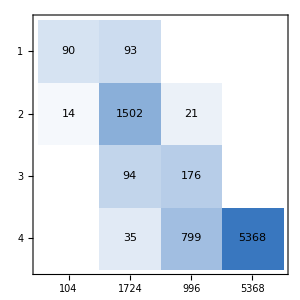
actual class | -Graphics-
 | predicted class

```mathematica
NetMeasurements[netECA4,fullTestSetBigC,"ConfusionMatrixPlot"]
```

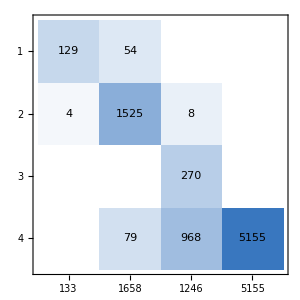
{0.864136,<|1→0.969925,2→0.919783,3→0.216693,4→1.|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA5, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

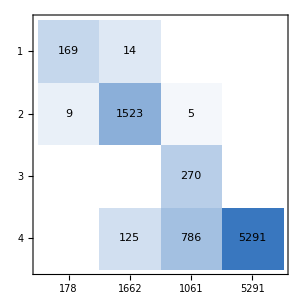
{0.885376,<|1→0.949438,2→0.916366,3→0.254477,4→1.|>,actual class | -Graphics-
 | predicted class}

```mathematica
NetMeasurements[netECA6, fullTestSetBigC, {"Accuracy", "Precision", "ConfusionMatrixPlot"}]
```

### Checking highest- and lowest-entropy images in test set for Network IV

```mathematica
entropyImagesBigC=RandomSample[Keys[fullTestSetBigC],500];
entropiesBigC=netECA4[entropyImagesBigC,"Entropy"];
highEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,-10]]]
lowEntBigC=entropyImagesBigC[[Ordering[entropiesBigC,10]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Thread[highEntBigC->netECA4[highEntBigC]]
Thread[lowEntBigC->netECA4[lowEntBigC]]
```

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2}

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

### Checking Entropy for Network V

```mathematica
entropyImagesBigC5=RandomSample[Keys[fullTestSetBigC],2000];
entropiesBigC5=netECA5[entropyImagesBigC5,"Entropy"];
highEntBigC5=entropyImagesBigC5[[Ordering[entropiesBigC5,-10]]]
lowEntBigC5=entropyImagesBigC5[[Ordering[entropiesBigC5,10]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Thread[highEntBigC5->netECA5[highEntBigC5]]
Thread[lowEntBigC5->netECA5[lowEntBigC5]]
```

{-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→3}

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

### Checking Entropy for Network VI

```mathematica
entropyImagesBigC6=RandomSample[Keys[fullTestSetBigC],2000];
entropiesBigC6=netECA6[entropyImagesBigC6,"Entropy"];
highEntBigC6=entropyImagesBigC6[[Ordering[entropiesBigC6,-10]]]
lowEntBigC6=entropyImagesBigC6[[Ordering[entropiesBigC6,10]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Thread[highEntBigC6->netECA6[highEntBigC6]]
Thread[lowEntBigC6->netECA6[lowEntBigC6]]
```

{-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→1,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→4}

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→4}

### Testing Network IV on k=5/6, r=1 images

```mathematica
netECA4=Import["netECA4-22may-3.wlnet","WLNet"]
```

NetChain[<>]

```mathematica
testData5kr1C=data5T2C[10,200,120];
k5r1testC=Thread[testData5kr1C->netECA4[Keys@testData5kr1C]]
```

{(-Graphics-→555274587)→2,(-Graphics-→830440453)→2,(-Graphics-→256015586)→2,(-Graphics-→602299808)→3,(-Graphics-→537138645)→3,(-Graphics-→1018759951)→3,(-Graphics-→1183999995)→2,(-Graphics-→656480350)→3,(-Graphics-→275099445)→3,(-Graphics-→727878792)→3}

```mathematica
testData6kr1C = data6TC[10,200,120];
k6r1testC=Thread[testData6kr1C->netECA4[Keys@testData6kr1C]]
```

{(-Graphics-→1369280495157)→2,(-Graphics-→695147763153)→3,(-Graphics-→230820111692)→2,(-Graphics-→1786908954663)→3,(-Graphics-→1721005408527)→4,(-Graphics-→1876955187335)→3,(-Graphics-→2784813723143)→3,(-Graphics-→2435317049084)→3,(-Graphics-→1363396903494)→3,(-Graphics-→244892860791)→3}

### Testing network V on k=5/6, r=1 images

```mathematica
testData5kr1C5=data5T2C[20,200,120];
k5r1testC5=Thread[testData5kr1C5->netECA5[Keys@testData5kr1C5,{"TopProbabilities",2}]]
```

{(-Graphics-→648626494)→{2→0.0899356,4→0.907522},(-Graphics-→36969296)→{3→0.234358,4→0.765633},(-Graphics-→1164564486)→{4→0.000149515,3→0.99985},(-Graphics-→968895016)→{3→0.151381,4→0.848617},(-Graphics-→1041243317)→{4→0.0000845454,3→0.999913},(-Graphics-→679678365)→{3→0.0743836,2→0.901006},(-Graphics-→662375822)→{4→0.00157124,3→0.998327},(-Graphics-→622524470)→{3→0.37217,2→0.439608},(-Graphics-→310548859)→{3→0.1657,4→0.83423},(-Graphics-→381985281)→{2→0.204319,4→0.795246},(-Graphics-→155701712)→{4→0.145092,3→0.854907},(-Graphics-→514511817)→{4→0.0777484,2→0.916331},(-Graphics-→610750963)→{2→0.0018545,4→0.99744},(-Graphics-→97274978)→{4→0.00194351,2→0.997739},(-Graphics-→1081515933)→{2→0.00497279,4→0.995},(-Graphics-→101707725)→{4→0.388398,3→0.611587},(-Graphics-→593680512)→{4→0.000306886,3→0.999529},(-Graphics-→777716689)→{3→0.279784,4→0.71969},(-Graphics-→497757880)→{3→0.0234419,4→0.976438},(-Graphics-→364102552)→{4→0.0343015,2→0.96568}}

```mathematica
testData6kr1C5 = data6TC[20,200,120];
k6r1testC5=Thread[testData6kr1C5->netECA5[Keys@testData6kr1C5,{"TopProbabilities",2}]]
```

{(-Graphics-→2140322472981)→{4→0.385685,3→0.614177},(-Graphics-→2393914643526)→{4→0.0210504,3→0.978483},(-Graphics-→2053201776355)→{3→0.163982,2→0.714814},(-Graphics-→752141048566)→{4→0.107666,3→0.892334},(-Graphics-→1633214012187)→{3→0.256557,4→0.743419},(-Graphics-→205987104993)→{2→0.117551,4→0.882448},(-Graphics-→1677728204097)→{4→5.64455×10^-6,3→0.999994},(-Graphics-→2107263754397)→{4→0.082527,3→0.917473},(-Graphics-→1930003590251)→{4→0.106348,3→0.89365},(-Graphics-→2389529132771)→{3→0.00768888,4→0.992307},(-Graphics-→1709821319577)→{4→0.0175132,3→0.982487},(-Graphics-→1034507802034)→{2→0.35561,4→0.64424},(-Graphics-→1192465516957)→{3→0.0268969,4→0.970458},(-Graphics-→2661787172664)→{4→0.0404416,3→0.959429},(-Graphics-→847748942279)→{4→0.0713072,2→0.927012},(-Graphics-→1032388414942)→{4→0.00969077,3→0.990309},(-Graphics-→1666004891517)→{4→6.70879×10^-6,3→0.999993},(-Graphics-→2478541394776)→{4→0.277771,3→0.690083},(-Graphics-→932645253063)→{3→0.207994,4→0.792006},(-Graphics-→337558272813)→{4→0.134153,3→0.865846}}

### Testing network VI on k=5/6, r=1 images

```mathematica
testData5kr1C6=data5T2C[20,200,120];
k5r1testC6=Thread[testData5kr1C6->netECA6[Keys@testData5kr1C6,{"TopProbabilities",2}]]
```

{(-Graphics-→57818283)→{4→0.0000238117,2→0.999973},(-Graphics-→1044867935)→{4→3.3046×10^-6,2→0.999997},(-Graphics-→480340855)→{2→0.0943981,4→0.891295},(-Graphics-→1108453625)→{4→2.68196×10^-9,2→1.},(-Graphics-→1188797638)→{4→0.44402,3→0.55598},(-Graphics-→194226008)→{4→0.209606,3→0.787397},(-Graphics-→750353946)→{4→0.0625052,3→0.937488},(-Graphics-→971654562)→{3→0.000554937,2→0.999},(-Graphics-→780837716)→{2→0.000975013,4→0.998843},(-Graphics-→1068887710)→{3→0.214754,4→0.782422},(-Graphics-→409160639)→{3→0.000406241,4→0.999593},(-Graphics-→64616370)→{4→0.203775,3→0.795874},(-Graphics-→935443699)→{2→0.00526674,4→0.994731},(-Graphics-→655296617)→{3→0.0666499,4→0.933317},(-Graphics-→693095807)→{4→0.149592,3→0.850377},(-Graphics-→950965544)→{4→0.137234,2→0.859277},(-Graphics-→565424043)→{4→0.336171,2→0.661287},(-Graphics-→265460035)→{4→0.440836,3→0.559164},(-Graphics-→942021430)→{3→0.0994604,2→0.900525},(-Graphics-→319713877)→{3→0.186876,4→0.813122}}

```mathematica
testData6kr1C6 = data6TC[20,200,120];
k6r1testC6=Thread[testData6kr1C6->netECA6[Keys@testData6kr1C6,{"TopProbabilities",2}]]
```

{(-Graphics-→1207010117645)→{4→0.00831573,3→0.991479},(-Graphics-→322146672175)→{2→0.0748844,4→0.92511},(-Graphics-→2608753185152)→{3→0.168331,4→0.790787},(-Graphics-→2592706257887)→{4→0.0294994,3→0.9705},(-Graphics-→1053338235394)→{4→0.178319,3→0.818732},(-Graphics-→1044114503140)→{4→0.0410611,3→0.958927},(-Graphics-→564898470856)→{4→0.0359682,3→0.964014},(-Graphics-→2666816750422)→{3→0.0384538,4→0.961546},(-Graphics-→2743020733306)→{2→0.0124328,4→0.986006},(-Graphics-→1661403844932)→{2→0.0980948,3→0.895002},(-Graphics-→1941732867200)→{3→0.0000540623,4→0.999946},(-Graphics-→1931468347465)→{4→0.431502,3→0.560876},(-Graphics-→1190433074497)→{2→0.00265841,4→0.997045},(-Graphics-→2308189821626)→{4→0.113693,3→0.884634},(-Graphics-→18345165990)→{2→0.122598,3→0.820363},(-Graphics-→1214767416307)→{3→0.00107258,4→0.998335},(-Graphics-→972231004329)→{4→0.128884,3→0.871115},(-Graphics-→1459828799229)→{3→0.0429323,4→0.934185},(-Graphics-→1613375044836)→{3→0.221142,4→0.778858},(-Graphics-→226868632354)→{4→0.22783,3→0.77217}}

```mathematica
tempNet1=Take[NetModel["Inception V3 Trained on ImageNet Competition Data"],{1,-4}]
newNet1=NetChain[<|"pretrainedNet"->tempNet1,"linearNew"->LinearLayer[],"softmax"->SoftmaxLayer[]|>,"Output"->NetDecoder[{"Class",Range[1,4]}]]
trainedNet1=NetTrain[newNet1,fullTrainingBigC3,LearningRateMultipliers->{"linearNew"->1,_->0}]
```

NetChain[<>]

NetChain[<>]

NetChain[<>]